# Legendre & Scaled Legendre Polynomials

By Manuel A. Diaz, NTU, 2012.07.10

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook Background

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Set Notebook background back to default

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

## Legendre Polynomials

#### The Legendre Polynomials

According any undergraduate textbooks, the most convenient way to compute the Legendre Polynomials is by using Rodriguez formula:

```mathematica
Subscript[P, l_][x_]:=1/(2^l l!)D[(x^2-1)^l, {x,l}]
```

```mathematica
Table[Subscript[P, l][x],{l,0,5}] //Simplify//Column
```

1
x
1/2 (-1+3 x^2)
1/2 x (-3+5 x^2)
1/8 (3-30 x^2+35 x^4)
1/8 x (15-70 x^2+63 x^4)

The Rodriguez formula works for non-negative integers values of l.

In Mathematica we have a build in function that help us to do the same,

```mathematica
legendreP =Table[LegendreP[i,𝒳],{i,0,6}];
Column[legendreP] // TraditionalForm
```

1
𝒳
1/2 (3 𝒳^2-1)
1/2 (5 𝒳^3-3 𝒳)
1/8 (35 𝒳^4-30 𝒳^2+3)
1/8 (63 𝒳^5-70 𝒳^3+15 𝒳)
1/16 (231 𝒳^6-315 𝒳^4+105 𝒳^2-5)

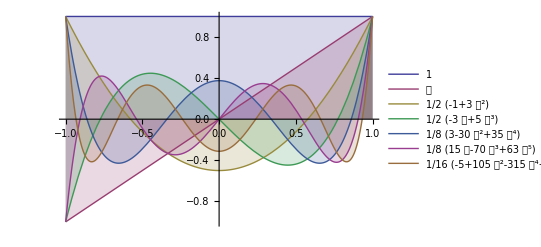

```mathematica
Plot[Evaluate[legendreP],{𝒳,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

## Scaled Legendre Polynomials

Define the size of our interval, I_j, as Δx_j. This interval and it will be identified by its middel point x_j. Notice that our basis polynomials work on the range of [-1,1]. Thus we are now interested in finding a way to scale them to and dimensionless interval I_j with range [-1/2,1/2].

The first idea to scale them is by making the change of variable 𝒳 → (x-x_j)/Δx_j, and using grand Schmidt ortogonalization process to build a new set or orthogonal polynomials.

### Initialize Notation

```mathematica
Needs["Notation`"]
```

based on http://en.wikipedia.org/wiki/Gram-Schmidt_process, we configure:

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-1/2,1/2}]]
```

```mathematica
Notation[Subscript[proj, u_][v_] ⟹ (<u_,v_>)/(<u_,u_>)u_]
```

Testing:

```mathematica
<Subscript[v, 1][z],Subscript[v, 1][z]>
```

∫_(-1/2)^(1/2) v_1[z]^2 ⅆz

```mathematica
<a z,z>
```

a/12

```mathematica
(<a[z],b[z]>)/(<a[z],a[z]>)a[z] == Subscript[proj, a[z]][b[z]]
```

True

```mathematica
Symbolize[Subscript[Δx, j]]; Symbolize[Subscript[x, j]];Symbolize[Subscript[I, j]];
```

### Building Scaled Legendre Polynomials using Gram Schmidt Orthogonalization process

#### Procedure 1: (not so good...)

based on http : // en.wikipedia.org/wiki/Gram - Schmidt_process, we configure :

Defining our initial vectors,

```mathematica
Table[Subscript[v, i]=z^i,{i,0,6}](* here z = x-Subscript[x, j] *)
```

{1,z,z^2,z^3,z^4,z^5,z^6}

Compute initial projection

```mathematica
Subscript[u, 0]=Subscript[v, 0]
```

1

```mathematica
Subscript[u, 1]=Subscript[v, 1]-Subscript[proj, Subscript[u, 0]][Subscript[v, 1]]
```

z

```mathematica
scaledLegendre = Table[Subscript[u, i+1]=Subscript[v, i+1]-Subscript[proj, Subscript[u, i-1]][Subscript[v, i+1]] -Subscript[proj, Subscript[u, i]][Subscript[v, i+1]],{i,1,5}] ;
```

```mathematica
scaledLegendre /. z -> (x-Subscript[x, j])/Subscript[Δx, j]//Simplify// Column
```

-1/12+(x-x_j)^2/Δx_j^2
(x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j)
-3/14 (-1/12+(x-x_j)^2/Δx_j^2)+(x-x_j)^4/Δx_j^4
-5/18 ((x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j))+(x-x_j)^5/Δx_j^5
-(885 (-3/14 (-1/12+(x-x_j)^2/Δx_j^2)+(x-x_j)^4/Δx_j^4))/4444+(x-x_j)^6/Δx_j^6

#### Procedure 2: (way much better)

based on http : // mathworld.wolfram.com/Gram - SchmidtOrthonormalization.html, we configure :

```mathematica
Subscript[p, 0]=1;
Subscript[p, 1]=(z - (<z Subscript[p, 0],Subscript[p, 0]>)/(<Subscript[p, 0],Subscript[p, 0]>))Subscript[p, 0];
```

```mathematica
scaledLegendre=Table[Subscript[p, i+1]=(z - (<z Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i],Subscript[p, i]>))Subscript[p, i] -(<Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i-1],Subscript[p, i-1]>)Subscript[p, i-1] ,{i,1,6}]//Expand ;
```

```mathematica
scaledLegendre = Join[{Subscript[p, 0],Subscript[p, 1]},scaledLegendre];
```

```mathematica
scaledLegendre //Column
```

1
z
-1/12+z^2
-(3 z)/20+z^3
3/560-(3 z^2)/14+z^4
(5 z)/336-(5 z^3)/18+z^5
-5/14784+(5 z^2)/176-(15 z^4)/44+z^6
-(35 z)/27456+(105 z^3)/2288-(21 z^5)/52+z^7

How about using rewritting in the form z = (x-x_j)/Δx_j. we have,

```mathematica
scaledLegendre /.z->(x-Subscript[x, j])/Subscript[Δx, j]//Column
```

1
(x-x_j)/Δx_j
-1/12+(x-x_j)^2/Δx_j^2
(x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j)
3/560+(x-x_j)^4/Δx_j^4-(3 (x-x_j)^2)/(14 Δx_j^2)
(x-x_j)^5/Δx_j^5-(5 (x-x_j)^3)/(18 Δx_j^3)+(5 (x-x_j))/(336 Δx_j)
-5/14784+(x-x_j)^6/Δx_j^6-(15 (x-x_j)^4)/(44 Δx_j^4)+(5 (x-x_j)^2)/(176 Δx_j^2)
(x-x_j)^7/Δx_j^7-(21 (x-x_j)^5)/(52 Δx_j^5)+(105 (x-x_j)^3)/(2288 Δx_j^3)-(35 (x-x_j))/(27456 Δx_j)

which is in total agreement with the polynomials used in “RKDG for conservation laws II”, paper of 1989.
Now observe their orthogonality behavior,

```mathematica
Table[(<scaledLegendre[[i]],scaledLegendre[[j]]>),{i,1,7},{j,1,7}] //TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/12 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/180 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2800 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/44100 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/698544 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/11099088

we observe that they are indeed orthogonal but not orthonormal. We then need to define normalization contatns

```mathematica
ClearAll[a]
```

```mathematica
Diagonal[Table[Subscript[a, n,m]=(<Subscript[p, n],Subscript[p, m]>),{n,0,6},{m,0,6}]]
```

{1,1/12,1/180,1/2800,1/44100,1/698544,1/11099088}

Make a double check

```mathematica
Table[1/Subscript[a, n,n](<Subscript[p, n],Subscript[p, n]>),{n,0,6}]
```

{1,1,1,1,1,1,1}

Now in this form we have scaled orthogonal polynomials! ; )

#### Procedure 3: (the mathematica way)

```mathematica
scaledLegendre3 = Orthogonalize[{1,z,z^2,z^3,z^4,z^5,z^6},Integrate[#1 #2,{z,-1/2,1/2}]&] //Expand;
```

```mathematica
scaledLegendre3 //Column
```

1
2 √3 z
-(√5)/2+6 √5 z^2
-3 √7 z+20 √7 z^3
9/8-45 z^2+210 z^4
(15 √11 z)/4-70 √11 z^3+252 √11 z^5
-(5 √13)/16+(105 √13 z^2)/4-315 √13 z^4+924 √13 z^6

Observe their Orthogonality behavior,

```mathematica
Table[(<scaledLegendre3[[i]],scaledLegendre3[[j]]>),{i,1,7},{j,1,7}] //TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1

These are already orthonormal polynomials!

### Plot Scaled Legendre Polynomials

So, having this scaled functions we can think on using them as basis functions to expand otherpolynomials just as we did in classical Finite Element Methods,

First we plot the scaled polynomials that professor Cockburn and Shu are using in their publications,

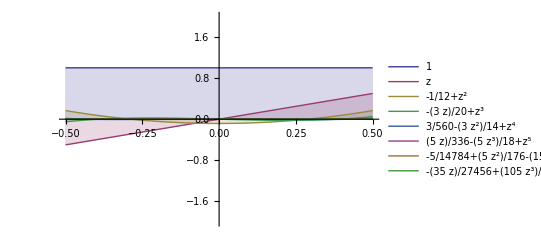

```mathematica
orthogonalpolinomials = scaledLegendre ;
Plot[Evaluate[orthogonalpolinomials],{z,-1/2,1/2},
Filling->Axis,PlotLegends->"Expressions",PlotRange->{-2,2}]
```

Comparing to the polynomials we have derived with mathematica orthogonal function,

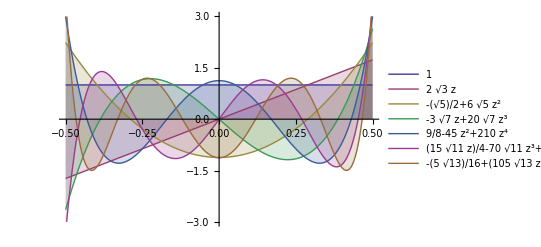

```mathematica
orthogonalpolinomials = scaledLegendre3;
Plot[Evaluate[orthogonalpolinomials],{z,-1/2,1/2},
Filling->Axis,PlotLegends->"Expressions",PlotRange->{-3,3}]
```

We can observe that their behavior is totally different for the same dimensionless intervale: I: [-1/2,1/2].

### Derivative of the scaled polynomials

```mathematica
dscaledpolynomials = D[scaledLegendre,z];
dscaledpolynomials /.z -> (x-Subscript[x, j])/Subscript[Δx, j] //Column
```

0
1
(2 (x-x_j))/Δx_j
-3/20+(3 (x-x_j)^2)/Δx_j^2
(4 (x-x_j)^3)/Δx_j^3-(3 (x-x_j))/(7 Δx_j)
5/336+(5 (x-x_j)^4)/Δx_j^4-(5 (x-x_j)^2)/(6 Δx_j^2)
(6 (x-x_j)^5)/Δx_j^5-(15 (x-x_j)^3)/(11 Δx_j^3)+(5 (x-x_j))/(88 Δx_j)
-35/27456+(7 (x-x_j)^6)/Δx_j^6-(105 (x-x_j)^4)/(52 Δx_j^4)+(315 (x-x_j)^2)/(2288 Δx_j^2)

```mathematica
Table[Subscript[dp, i]= dscaledpolynomials[[i+1]],{i,0,7}];
```

```mathematica
dcoefficients = Table[Subscript[b, n,m]= (<Subscript[p, n],Subscript[dp, m]>),{n,0,7},{m,0,7}];
dcoefficients //TableForm
```

0 | 1 | 0 | 1/10 | 0 | 1/126 | 0 | 1/1716
0 | 0 | 1/6 | 0 | 1/70 | 0 | 1/924 | 0
0 | 0 | 0 | 1/60 | 0 | 1/756 | 0 | 1/10296
0 | 0 | 0 | 0 | 1/700 | 0 | 1/9240 | 0
0 | 0 | 0 | 0 | 0 | 1/8820 | 0 | 1/120120
0 | 0 | 0 | 0 | 0 | 0 | 1/116424 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/1585584
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0